## Final wave form

### Amp1

```mathematica
wf1mm=Import[NotebookDirectory[]<>"amplitude_frequency_1MMspline.txt","Table"];
```

```mathematica
wf1mmRe=Table[wf1mm[[ii,1;;2]],{ii,201,Length@wf1mm}];
wf1mmIm=Table[wf1mm[[ii,{1,3}]],{ii,201,Length@wf1mm}];
```

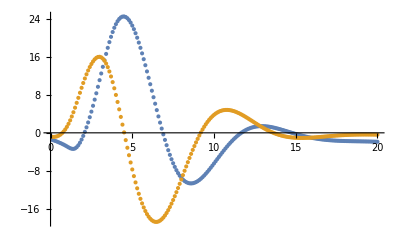

```mathematica
ListPlot[{wf1mmRe,wf1mmIm},PlotRange->All]
```

```mathematica
num//Length
```

200

```mathematica
omegas//Length
```

200

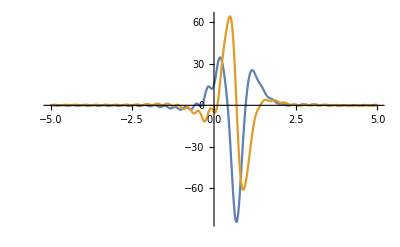

```mathematica
num=Table[wf1mm[[ii,2]]+I wf1mm[[ii,3]],{ii,201,Length@wf1mm}];
omegas=wf1mm[[201;;-1,1]];
expNum=Table[Exp[I  x t],{x,wf1mmRe[[1,1]],wf1mmRe[[-1,1]],0.1}];
wfTime=1/20(num.expNum);
Plot[{Re[%],Im[%]},{t,-5,5},PlotRange->All]
```

#### Soft part

```mathematica
amp1w0new=(9 √3)/(1024 √(zb^2+zv^2))+(171 (-4 ⅈ+√3) zb)/(2048 √2 √(zb^2+zv^2) ω)+(zb (36-369 ⅈ √3+7 ((-15-36 ⅈ)+(9+20 ⅈ) √3) π+7 (52-19 ⅈ √3) Log[4]+504 ⅈ Log[2+√3]-392 √3 Log[2+√3]))/(768 √2 π (zb^2+zv^2));
amp1w0reg=amp1w0new/.(zb^2+zv^2):>(zb^2+zv^2+ω^2);
amp1w0regIntzb=Assuming[b<0,√(2 π)FourierTransform[amp1w0reg,zb,b]];
amp1w0regIntzb=Assuming[zv>0&&ω>0,amp1w0regIntzb/.b->-1//Simplify]
```

1/6144(108 √3 BesselK[0,√(zv^2+ω^2)]+√2 (-(513 ⅈ (-4 ⅈ+√3) √(zv^2+ω^2) BesselK[1,√(zv^2+ω^2)])/ω+4 ⅇ^(-√(zv^2+ω^2)) (-36 ⅈ-369 √3-7 ⅈ ((-15-36 ⅈ)+(9+20 ⅈ) √3) π-7 (52 ⅈ+19 √3) Log[4]+504 Log[2+√3]+392 ⅈ √3 Log[2+√3])))

```mathematica
Monitor[wf1listReg=Table[amp1w0regIntzbNum=ω^2*amp1w0regIntzb/.ω->ii;NIntegrate[amp1w0regIntzbNum,{zv,0,∞},Method->"LocalAdaptive"],{ii,omegas}];,ii]
```

```mathematica
wf1RegIm=Table[{0.1*ii,Im[wf1listReg[[ii]]]},{ii,Length@wf1listReg}];
wf1RegRe=Table[{0.1*ii,Re[wf1listReg[[ii]]]},{ii,Length@wf1listReg}];
```

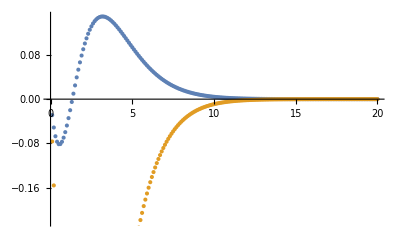

```mathematica
ListPlot[{wf1RegIm,wf1RegRe}]
```

#### Total

```mathematica
wf1FinalIm=MapThread[Plus,{wf1mmIm,Times[#,{0,1}]&/@wf1RegIm}];
wf1FinalRe=MapThread[Plus,{wf1mmRe,Times[#,{0,1}]&/@wf1RegRe}];
```

```mathematica
{wf1FinalIm,wf1RegIm,wf1mmIm}>>NotebookDirectory[]<>"wf1AllImmm.txt";
{wf1FinalRe,wf1RegRe,wf1mmRe}>>NotebookDirectory[]<>"wf1AllRemm.txt";
```

```mathematica
(*{wfImFull,wfRegIm,wf1Im}>>NotebookDirectory[]<>"wf1Im.txt";
{wfReFull,wfRegRe,wf1Re}>>NotebookDirectory[]<>"wf1Re.txt";*)
```

```mathematica
{wf1FinalIm,wf1RegIm,wf1mmIm}=Get[NotebookDirectory[]<>"wf1AllImmm.txt"];
{wf1FinalRe,wf1RegRe,wf1mmRe}=Get[NotebookDirectory[]<>"wf1AllRemm.txt"];
```

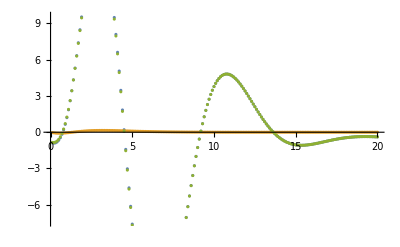

```mathematica
ListPlot[{wf1FinalIm,wf1RegIm,wf1mmIm}]
```

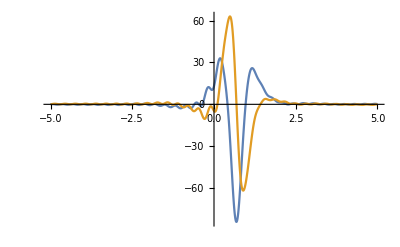

```mathematica
num=Table[wf1FinalRe[[ii,2]]+I wf1FinalIm[[ii,2]],{ii,Length@wf1FinalRe}];
expNum=Table[Exp[I  x t],{x,omegas}];
wfTime=1/20(num.expNum);
Plot[{Re[%],Im[%]},{t,-5,5},PlotRange->All]
```

### Amp2

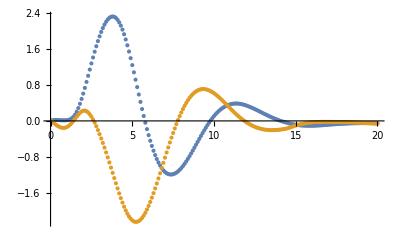

```mathematica
wf2mm=Import[NotebookDirectory[]<>"amplitude_frequency_2MMspline.txt","Table"];
wf2mmRe=Table[wf2mm[[ii,1;;2]],{ii,201,Length@wf2mm}];
wf2mmIm=Table[wf2mm[[ii,{1,3}]],{ii,201,Length@wf2mm}];
ListPlot[{wf2mmRe,wf2mmIm},PlotRange->All]
```

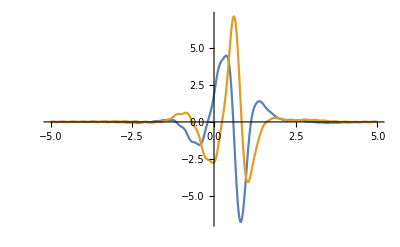

```mathematica
num=Table[wf2mm[[ii,2]]+I wf2mm[[ii,3]],{ii,201,Length@wf2mm}];
omegas=wf2mm[[201;;-1,1]];
expNum=Table[Exp[I  x t],{x,omegas}];
wfTime=1/20(num.expNum);
Plot[{Re[%],Im[%]},{t,-5,5},PlotRange->All]
```

#### Soft part

```mathematica
amp2w0new=(9 √3)/(1024 √(zb^2+zv^2))+(171 (-4 ⅈ+√3) zb)/(2048 √2 √(zb^2+zv^2) ω)+(zb (-552+240 ⅈ √3+7 ((-15-36 ⅈ)+(9+20 ⅈ) √3) π+7 ⅈ (52 ⅈ+19 √3) Log[4]-714 ⅈ Log[2+√3]+112 √3 Log[2+√3]))/(384 √2 π (zb^2+zv^2));
amp2w0reg=amp2w0new/.(zb^2+zv^2):>(zb^2+zv^2+ω^2);
```

```mathematica
amp2w0regIntzb=Assuming[b<0,√(2 π)FourierTransform[amp2w0reg,zb,b]];
```

```mathematica
amp2w0regIntzb=Assuming[zv>0&&ω>0,amp2w0regIntzb/.b->-1//Simplify]
```

1/6144(108 √3 BesselK[0,√(zv^2+ω^2)]+√2 (-(513 ⅈ (-4 ⅈ+√3) √(zv^2+ω^2) BesselK[1,√(zv^2+ω^2)])/ω+8 ⅇ^(-√(zv^2+ω^2)) (552 ⅈ+240 √3-7 ⅈ ((-15-36 ⅈ)+(9+20 ⅈ) √3) π+7 (52 ⅈ+19 √3) Log[4]-714 Log[2+√3]-112 ⅈ √3 Log[2+√3])))

```mathematica
Monitor[wflistReg=Table[amp2w0regIntzbNum=ω^2*amp2w0regIntzb/.ω->ii;NIntegrate[amp2w0regIntzbNum,{zv,0,∞},Method->"LocalAdaptive"],{ii,omegas}];,ii]
```

```mathematica
wf2RegIm=Table[{0.1*ii,Im[wflistReg[[ii]]]},{ii,Length@wflistReg}];
wf2RegRe=Table[{0.1*ii,Re[wflistReg[[ii]]]},{ii,Length@wflistReg}];
```

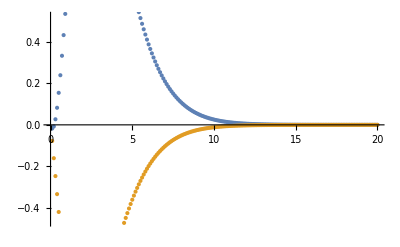

```mathematica
ListPlot[{wf2RegIm,wf2RegRe}]
```

#### Total

```mathematica
wf2FinalIm=MapThread[Plus,{wf2mmIm,Times[#,{0,1}]&/@wf2RegIm}];
wf2FinalRe=MapThread[Plus,{wf2mmRe,Times[#,{0,1}]&/@wf2RegRe}];
```

```mathematica
{wf2FinalIm,wf2RegIm,wf2mmIm}>>NotebookDirectory[]<>"wf2AllImmm.txt";
{wf2FinalRe,wf2RegRe,wf2mmRe}>>NotebookDirectory[]<>"wf2AllRemm.txt";
```

```mathematica
(*{wfImFull,wfRegIm,wf1Im}>>NotebookDirectory[]<>"wf1Im.txt";
{wfReFull,wfRegRe,wf1Re}>>NotebookDirectory[]<>"wf1Re.txt";*)
```

```mathematica
{wf2FinalIm,wf2RegIm,wf2mmIm}=Get[NotebookDirectory[]<>"wf2AllImmm.txt"];
{wf2FinalRe,wf2RegRe,wf2mmRe}=Get[NotebookDirectory[]<>"wf2AllRemm.txt"];
```

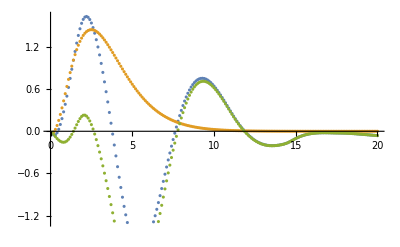

```mathematica
ListPlot[{wf2FinalIm,wf2RegIm,wf2mmIm}]
```

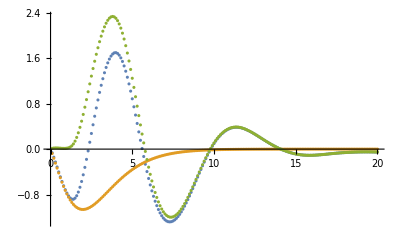

```mathematica
ListPlot[{wf2FinalRe,wf2RegRe,wf2mmRe},PlotRange->Automatic]
```

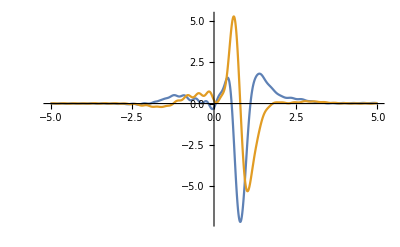

```mathematica
num=Table[wf2FinalRe[[ii,2]]+I wf2FinalIm[[ii,2]],{ii,Length@wf2FinalRe}];
expNum=Table[Exp[I  x t],{x,omegas}];
wfTime=1/20(num.expNum);
Plot[{Re[%],Im[%]},{t,-5,5},PlotRange->All]
```

```mathematica
num
```

{-0.0642146-0.0309872 ⅈ,-0.142313-0.0541181 ⅈ,-0.226459-0.0498967 ⅈ,-0.313696-0.021279 ⅈ,-0.401348+0.0285675 ⅈ,-0.487037+0.096571 ⅈ,-0.568686+0.179922 ⅈ,-0.644494+0.276167 ⅈ,-0.712913+0.383248 ⅈ,-0.772622+0.499517 ⅈ,-0.822137+0.623305 ⅈ,-0.858739+0.75164 ⅈ,-0.879497+0.881481 ⅈ,-0.881594+1.0101 ⅈ,-0.862305+1.13507 ⅈ,-0.819766+1.25382 ⅈ,-0.755283+1.36263 ⅈ,-0.670989+1.4576 ⅈ,-0.569046+1.53498 ⅈ,-0.451636+1.59114 ⅈ,-0.321075+1.62343 ⅈ,-0.180199+1.63266 ⅈ,-0.0319594+1.62056 ⅈ,0.120693+1.5889 ⅈ,0.274826+1.5395 ⅈ,0.427766+1.47414 ⅈ,0.577849+1.39449 ⅈ,0.723675+1.30216 ⅈ,0.863866+1.19876 ⅈ,0.997066+1.08589 ⅈ,1.12197+0.965006 ⅈ,1.23741+0.836982 ⅈ,1.34227+0.702532 ⅈ,1.43546+0.562345 ⅈ,1.51591+0.417088 ⅈ,1.5826+0.267508 ⅈ,1.6347+0.114748 ⅈ,1.67142-0.0399665 ⅈ,1.69201-0.195439 ⅈ,1.69572-0.350494 ⅈ,1.68202-0.503885 ⅈ,1.65127-0.653997 ⅈ,1.60403-0.799142 ⅈ,1.54088-0.937648 ⅈ,1.46241-1.06787 ⅈ,1.3694-1.18828 ⅈ,1.26338-1.29779 ⅈ,1.14607-1.39547 ⅈ,1.01919-1.48035 ⅈ,0.884485-1.55153 ⅈ,0.743692-1.60825 ⅈ,0.598582-1.65052 ⅈ,0.450937-1.67853 ⅈ,0.302543-1.69248 ⅈ,0.155187-1.69257 ⅈ,0.0105531-1.67915 ⅈ,-0.130089-1.65308 ⅈ,-0.265577-1.6154 ⅈ,-0.394743-1.5671 ⅈ,-0.516422-1.50923 ⅈ,-0.629625-1.44277 ⅈ,-0.734073-1.36867 ⅈ,-0.829668-1.28782 ⅈ,-0.91631-1.20116 ⅈ,-0.993899-1.10959 ⅈ,-1.06234-1.01402 ⅈ,-1.12152-0.915392 ⅈ,-1.17136-0.814608 ⅈ,-1.21174-0.71259 ⅈ,-1.24258-0.610259 ⅈ,-1.26388-0.508467 ⅈ,-1.27604-0.407808 ⅈ,-1.27957-0.308804 ⅈ,-1.27497-0.211982 ⅈ,-1.26276-0.117865 ⅈ,-1.24342-0.0269549 ⅈ,-1.21741+0.0603415 ⅈ,-1.18518+0.143638 ⅈ,-1.14716+0.222552 ⅈ,-1.10381+0.2967 ⅈ,-1.05558+0.365736 ⅈ,-1.003+0.429461 ⅈ,-0.946637+0.487713 ⅈ,-0.887031+0.54033 ⅈ,-0.824739+0.587153 ⅈ,-0.760308+0.62806 ⅈ,-0.694269+0.663069 ⅈ,-0.627147+0.692242 ⅈ,-0.559469+0.715636 ⅈ,-0.49176+0.733312 ⅈ,-0.424525+0.745363 ⅈ,-0.35817+0.752004 ⅈ,-0.29308+0.753481 ⅈ,-0.22964+0.750045 ⅈ,-0.168234+0.741942 ⅈ,-0.109229+0.729444 ⅈ,-0.0529271+0.712912 ⅈ,0.000389563+0.692727 ⅈ,0.0504372+0.669269 ⅈ,0.0969318+0.642923 ⅈ,0.139651+0.614058 ⅈ,0.178618+0.582977 ⅈ,0.213919+0.549976 ⅈ,0.245637+0.515344 ⅈ,0.273858+0.479375 ⅈ,0.298665+0.442363 ⅈ,0.320144+0.4046 ⅈ,0.338378+0.366381 ⅈ,0.35345+0.327998 ⅈ,0.365443+0.28975 ⅈ,0.374442+0.251929 ⅈ,0.38053+0.214831 ⅈ,0.383788+0.178751 ⅈ,0.384301+0.143986 ⅈ,0.382151+0.110833 ⅈ,0.377451+0.0795219 ⅈ,0.370447+0.0500251 ⅈ,0.361408+0.0222477 ⅈ,0.35061-0.00390133 ⅈ,0.338326-0.0285177 ⅈ,0.324807-0.0516639 ⅈ,0.310215-0.0732863 ⅈ,0.294686-0.0933062 ⅈ,0.278359-0.11164 ⅈ,0.261372-0.128205 ⅈ,0.243864-0.142947 ⅈ,0.225968-0.155913 ⅈ,0.207826-0.167176 ⅈ,0.189571-0.176807 ⅈ,0.171341-0.184879 ⅈ,0.153261-0.191465 ⅈ,0.13542-0.196629 ⅈ,0.117893-0.200436 ⅈ,0.100759-0.202951 ⅈ,0.0840921-0.204236 ⅈ,0.0679676-0.204363 ⅈ,0.0524408-0.203436 ⅈ,0.037568-0.201561 ⅈ,0.0234015-0.198847 ⅈ,0.00999461-0.195404 ⅈ,-0.00261646-0.191279 ⅈ,-0.0144665-0.186285 ⅈ,-0.0256091-0.18017 ⅈ,-0.0360983-0.172686 ⅈ,-0.0459857-0.163582 ⅈ,-0.0553053-0.152752 ⅈ,-0.0640077-0.14065 ⅈ,-0.072022-0.127872 ⅈ,-0.0792779-0.115017 ⅈ,-0.0857064-0.10268 ⅈ,-0.0912552-0.0913496 ⅈ,-0.0959514-0.0810845 ⅈ,-0.0998377-0.0718356 ⅈ,-0.102961-0.0635512 ⅈ,-0.105365-0.0561834 ⅈ,-0.107094-0.0496825 ⅈ,-0.108194-0.0439976 ⅈ,-0.108709-0.0390788 ⅈ,-0.108684-0.0348774 ⅈ,-0.108163-0.0313424 ⅈ,-0.107193-0.028425 ⅈ,-0.105817-0.0260742 ⅈ,-0.104081-0.0242422 ⅈ,-0.102028-0.0228771 ⅈ,-0.0997046-0.02193 ⅈ,-0.097154-0.0213509 ⅈ,-0.0944228-0.0210889 ⅈ,-0.091555-0.0210961 ⅈ,-0.0885954-0.0213216 ⅈ,-0.0855892-0.0217144 ⅈ,-0.0825812-0.0222266 ⅈ,-0.0796154-0.0228071 ⅈ,-0.0767369-0.0234072 ⅈ,-0.0739916-0.0239748 ⅈ,-0.0714235-0.0244619 ⅈ,-0.0690645-0.0248396 ⅈ,-0.0668948-0.0251669 ⅈ,-0.0648811-0.0255228 ⅈ,-0.0629916-0.0259895 ⅈ,-0.0611912-0.0266468 ⅈ,-0.059458-0.0275549 ⅈ,-0.0578048-0.0286917 ⅈ,-0.0562547-0.0300193 ⅈ,-0.0548317-0.0314957 ⅈ,-0.0535588-0.0330798 ⅈ,-0.052454-0.0347378 ⅈ,-0.0515163-0.0364607 ⅈ,-0.0507406-0.0382444 ⅈ,-0.0501219-0.0400859 ⅈ,-0.0496544-0.0419813 ⅈ,-0.0493318-0.0439256 ⅈ,-0.0491503-0.0459088 ⅈ,-0.0491039-0.0479169 ⅈ,-0.0491865-0.0499379 ⅈ,-0.0493941-0.0519579 ⅈ,-0.0497208-0.0539647 ⅈ,-0.0501604-0.0559465 ⅈ,-0.0507091-0.0578892 ⅈ,-0.0513609-0.0597808 ⅈ,-0.0521106-0.0616084 ⅈ}

## Full Waveform

```mathematica
{wf1FinalIm,wf1RegIm,wf1mmIm}=Get[NotebookDirectory[]<>"wf1AllImmm.txt"];
{wf1FinalRe,wf1RegRe,wf1mmRe}=Get[NotebookDirectory[]<>"wf1AllRemm.txt"];
```

```mathematica
{wf2FinalIm,wf2RegIm,wf2mmIm}=Get[NotebookDirectory[]<>"wf2AllImmm.txt"];
{wf2FinalRe,wf2RegRe,wf2mmRe}=Get[NotebookDirectory[]<>"wf2AllRemm.txt"];
```

```mathematica
wfFullRe=MapThread[Plus,{Times[#,{1,(1-μ )}]&/@wf1FinalRe,Times[#,{0,μ}]&/@wf2FinalRe}]//Simplify;
(*wfFullRe[[11]]=1/2(wfFullRe[[10]]+wfFullRe[[12]]);*)
```

```mathematica
wfFullIm=MapThread[Plus,{Times[#,{1,(1-μ )}]&/@wf1FinalIm,Times[#,{0,μ}]&/@wf2FinalIm}]//Simplify;
(*wfFullIm[[11]]=1/2(wfFullIm[[10]]+wfFullIm[[12]]);*)
```

```mathematica
Table[wfFullIm,{μ,0.1,0.9,0.2}][[5]]
```

{{0.1,1.70234},{0.2,0.0574741},{0.3,-0.462396},{0.4,-0.681083},{0.5,-0.772115},{0.6,-0.801015},{0.7,-0.793757},{0.8,-0.765702},{0.9,-0.726007},{1.,-0.68},{1.1,-0.631293},{1.2,-0.582101},{1.3,-0.533824},{1.4,-0.490351},{1.5,-0.448054},{1.6,-0.4079},{1.7,-0.370684},{1.8,-0.336915},{1.9,-0.306818},{2.,-0.280389},{2.1,-0.257465},{2.2,-0.237784},{2.3,-0.22103},{2.4,-0.206862},{2.5,-0.19494},{2.6,-0.18494},{2.7,-0.176565},{2.8,-0.169553},{2.9,-0.163678},{3.,-0.158746},{3.1,-0.154596},{3.2,-0.151089},{3.3,-0.148101},{3.4,-0.145523},{3.5,-0.143252},{3.6,-0.141191},{3.7,-0.139253},{3.8,-0.137353},{3.9,-0.13542},{4.,-0.133389},{4.1,-0.131211},{4.2,-0.128868},{4.3,-0.126243},{4.4,-0.123423},{4.5,-0.120368},{4.6,-0.117068},{4.7,-0.113537},{4.8,-0.10979},{4.9,-0.105848},{5.,-0.101727},{5.1,-0.0974906},{5.2,-0.0931669},{5.3,-0.088619},{5.4,-0.0840633},{5.5,-0.0793219},{5.6,-0.0748172},{5.7,-0.0701658},{5.8,-0.0665564},{5.9,-0.0609878},{6.,-0.0564876},{6.1,-0.0522818},{6.2,-0.0477551}}

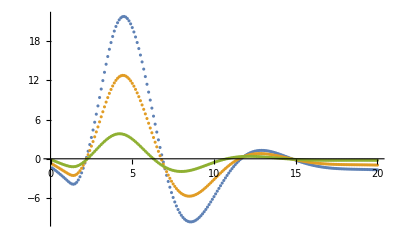

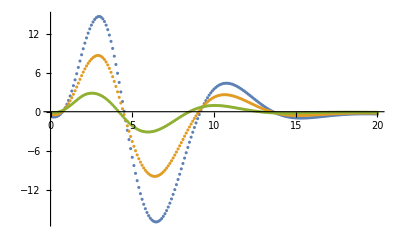

```mathematica
ListPlot[Table[wfFullRe,{μ,0.1,0.9,0.4}],PlotRange->All]
ListPlot[Table[wfFullIm,{μ,0.1,0.9,0.4}],PlotRange->All]
```

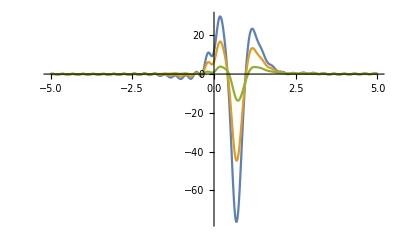

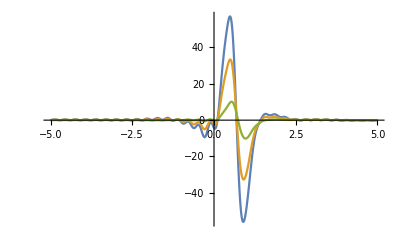

```mathematica
num=Table[wfFullRe[[ii,2]]+I wfFullIm[[ii,2]],{ii,Length@wfFullRe}];
expNum=Table[Exp[I  x t],{x,omegas}];
wfTime=1/20(num.expNum);
Plot[{Re[wfTime/.μ->0.1],Re[wfTime/.μ->0.5],Re[wfTime/.μ->0.9]},{t,-5,5},PlotRange->All]
Plot[{Im[wfTime/.μ->0.1],Im[wfTime/.μ->0.5],Im[wfTime/.μ->0.9]},{t,-5,5},PlotRange->All]
```